# Methods figures

Code for generating Fig. 1 (hypothesis setting with risk metrics) and Fig. 2 (TPC and time series) in the ‘Materials and Methods’ section.

## Risk Metrics

Run this code to generate Fig 1. The first block of code calculates the persistence boundaries and the second the number of time steps a population at carrying capacity can persist at any given negative growth rate.

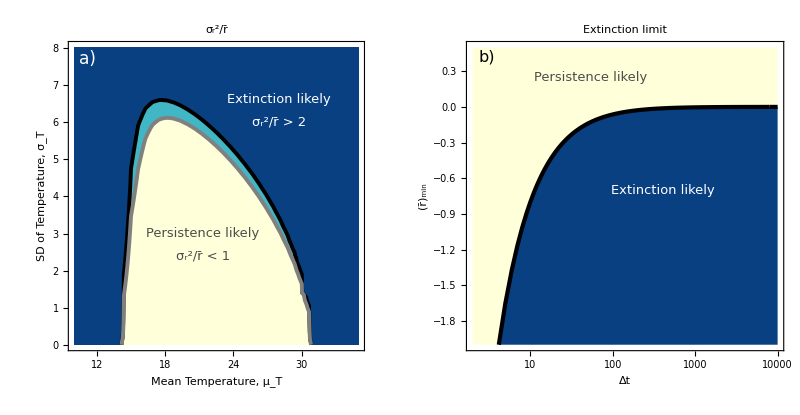

```mathematica
directory="/Users/alisonrobey/Documents/PhD Year 4 (2024-2025)/AutocorrelationExperiments/Final/Figures/";

lactin2[T_,{a_,b_,tmax_,δT_}]:=Exp[a T]-Exp[a tmax-((tmax-T)/δT)]+b;
paramsfit={0.044,-1.774,35.254,5.435};
w[T_]:=lactin2[T,paramsfit];

divisions=40;
σTrange=Range[0.01,8.01,8/divisions];
μTrange=Range[10,35,25/divisions];

Clear[T];
moments=Flatten[ParallelTable[Module[{mean,var,skew,kurt},
mean=NExpectation[w[T],T\[Distributed]NormalDistribution[μT,σT]];var=NExpectation[(w[T]-mean)^2,T\[Distributed]NormalDistribution[μT,σT]];
skew=NExpectation[((w[T]-mean))^3,T\[Distributed]NormalDistribution[μT,σT]]/var^(3/2);
kurt=NExpectation[(w[T]-mean)^4,T\[Distributed]NormalDistribution[μT,σT]]/(var^2)-3;
{μT,σT,mean,var,skew,kurt,If[mean>0,Log10[var/mean],10]}],{σT,σTrange},{μT,μTrange}],1];

persistenceboundaries2=ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{Log10[1],Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->{RGBColor["#ffffd9"],RGBColor["#41b6c4"],RGBColor["#084081"]},(*ColorFunction->newmap,*)ImageSize->280,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},PlotLabel->Style["σ_r^2/r̄",15],
Epilog->
{{Text[Style["a)",White,17],{11.2,7.7}]},
{Text[Style["Extinction likely",White,13],{28,6.6}]},
{Text[Style["Persistence likely",Darker[Darker[Lighter[Gray]]],13],{21.3,3}]},
{Text[Style["σ_r^2/r̄ > 2",White,13],{28,6}]},
{Text[Style["σ_r^2/r̄ < 1",Darker[Darker[Lighter[Gray]]],13],{21.3,2.4}]}}];

ExtTime[t_,α_,N0_]:=r/.NSolve[1==N0 r/α Exp[r t]/(((r/α)-N0)+N0 Exp[r t]),r,Reals][[1]];N0=5000;
α=0.0001;

extlimit2=ListLogLinearPlot[ParallelTable[{t,ExtTime[t,α,N0]},{t,2,9997}],ImageSize->300, AspectRatio->1,Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","(r̄)_min"},PlotStyle->{Thickness[0.01],Black},PlotRange->{{2,10000},{-2,.5}},PlotLabel->Style["Extinction limit",15],
Filling->{1->Top,1->Bottom},FillingStyle->{RGBColor["#ffffd9"],RGBColor["#084081"]},Joined->True,
Epilog->{Text[Style["b)",Black,16],{1.1,0.42}],
{Text[Style["Extinction likely",White,13],{6,-0.7}]},
{Text[Style["Persistence likely",Darker[Darker[Lighter[Gray]]],13],{4,0.25}]}}];

expectations=GraphicsRow[{persistenceboundaries2,extlimit2},Spacings->10,ImageSize->800]
Export[directory<>"Fig1.eps",expectations,"EPS",ImageResolution->1000];
```

## Thermal Performance Curve

Run this code to plot the data and lactin2 TPC fit for P. caudatum (Fig. 2a). You will first need to download ‘PcaudatumTPCdata.csv.’

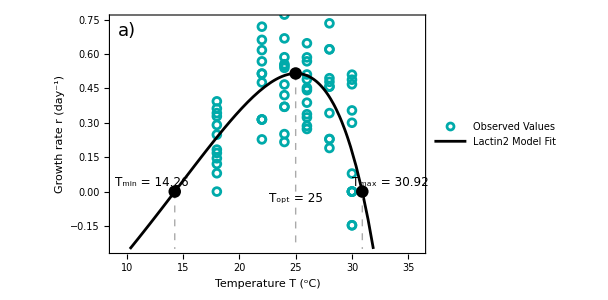

```mathematica
observed=Import[directory<>"PcaudatumTPCdata.csv"];
data=ListPlot[observed,PlotStyle->Darker[Cyan],PlotMarkers->{Graphics[Circle[],ImageSize->8]},PlotLegends->Placed[{Style["Observed Values",12,Darker[Gray]]},Scaled[{0.23,0.94}]],
PlotRange->{{9,36},{-0.25,0.75}},Frame->{True,True,False,False},PlotStyle->Black,ImageSize->imagesize,FrameStyle->16,AspectRatio->1/1.5,FrameLabel->{"Temperature T (^oC)","Growth rate r (day^-1)"},
Epilog->{{Text[Style["T_opt = 25",Black,12],{25,-.03}]},{Text[Style["T_min = 14.26",Black,12],{Tmin-2,.04}]},{Text[Style["T_max = 30.92",Black,12],{Tmax+2.5,.04}]},
Lighter[Gray],Dashed,Line[{{25,0},{25,0.515}}],Line[{{25,-.07},{25,-.25}}],Line[{{Tmin,0},{Tmin,-.25}}],Line[{{Tmax,0},{Tmax,-.25}}],
{Black,PointSize[0.02],Point[{Tmin,0}]},
{Black,PointSize[0.02],Point[{Tmax,0}]},{Black,PointSize[0.02],Point[{25,0.515}]},
Text[Style["a)",Black,18],{10,0.7}]}];

lactin2[T_,{a_,b_,tmax_,δT_}]:=Exp[a T]-Exp[a tmax-((tmax-T)/δT)]+b;
paramsfit={0.044,-1.774,35.254,5.435};
w[T_]:=lactin2[T,paramsfit];

imagesize=450;
prange={{0,35},{-0.2,.9}};
TPC=Show[Plot[lactin2[T,paramsfit],{T,10,35},PlotRange->{-0.25,0.75},Frame->{True,True,False,False},PlotStyle->Black,ImageSize->imagesize,FrameStyle->16,AspectRatio->1/1.5,FrameLabel->{"Temperature T (^oC)","Growth rate r (day^-1)"},PlotLegends->Placed[{Style["Lactin2 Model Fit",12,Darker[Gray]]},Scaled[{0.23,0.84}]]]];

TPCplot=Show[data,TPC]
```

## Temperature Time Series

Use this code create temperature time series with spectral synthesis and spectral mimicry, then check what the resulting spectral exponent is. Because we are creating a very short time series (112 long) and keeping the values consistent with mimicry, there is some variation in the resulting values of the spectral exponent (shown in the final three output lines, where equations are b - γx). For the experimental time series, this code was rerun several times until series with spectral exponents very close to the desired values were found.

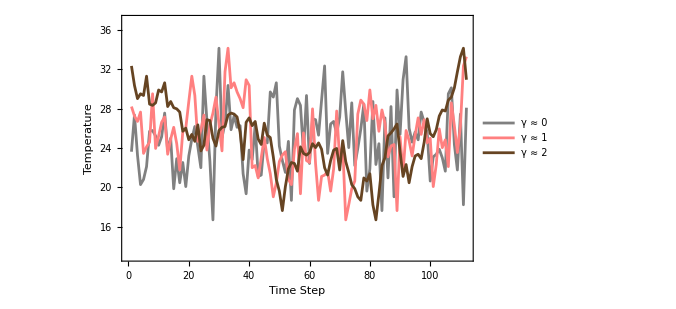

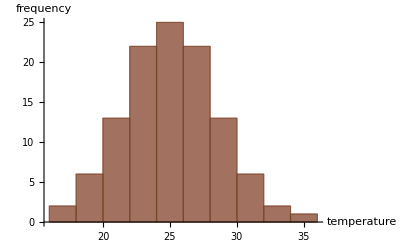

2.57738-0.29824 x

5.37194-1.22269 x

5.67329-1.67385 x

```mathematica
cmplx[mod_,arg_]:=ExpToTrig[mod Exp[I arg]];

SpecSynFourier[γ_,Nobs_,μ_:0,σ_:1,seed_:0]:=Module[{
phase,f,vec},
If[seed==0,SeedRandom[],SeedRandom[seed]];
phase=RandomReal[{0,2Pi},Nobs];
f=Range[1/Nobs,1,1/Nobs];
vec=InverseFourier[Join[{0+0I},Table[cmplx[1/(f[[i]]^(γ/2)),phase[[i]]],{i,1,(Nobs-1)}]],FourierParameters->{-1,1}];
Standardize[Re[vec]]*σ+μ];

Mimic1[x_,z_]:=Module[{y},
y=x;
Do [y[[Ordering[z,i][[i]]]]=x[[i]],{i,1,Length[x]}];
y];

γvals=Range[0,2,1]; 
μTvals=Range[25,25,1]; 
σTvals=Range[3.5,3.5,1]; 
tmax=112;

W=ConstantArray[0,{Length[μTvals],Length[σTvals],tmax}];
Do[W[[i,j,k]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],k*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]},{k,1,tmax-1}]
Do[W[[i,j,tmax]]=InverseCDF[NormalDistribution[μTvals[[i]],σTvals[[j]]],(tmax-.5)*(1/tmax)],{i,1,Length[μTvals]},{j,1,Length[σTvals]}];

X=SpecSynFourier[γvals[[1]],tmax];
Z0=Mimic1[W[[1,1]],X];
X=SpecSynFourier[γvals[[2]],tmax];
Z1=Mimic1[W[[1,1]],X];
X=SpecSynFourier[γvals[[3]],tmax];
Z2=Mimic1[W[[1,1]],X];

ListLinePlot[{Z0,Z1,Z2},PlotLegends->{"γ ≈ 0","γ ≈ 1","γ ≈ 2"},PlotRange->{13,37},PlotStyle->{Gray,Pink,Darker[Brown]},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Time Step","Temperature"},ImageSize->500]
Histogram[{Z0,Z1,Z2},ChartStyle->{Gray,Pink,Darker[Brown]},AxesLabel->{"temperature","frequency"}]

lt=Flatten[Abs[Fourier[{Z0}]]^2];
lt=Drop[lt,-Length[lt]/2];
lt=Drop[lt,1];
lt0=MapIndexed[{#2[[1]],#1}&,lt];
fit0=Fit[Log[lt0],{1,x},x]

lt=Flatten[Abs[Fourier[{Z1}]]^2];
lt=Drop[lt,-Length[lt]/2];
lt=Drop[lt,1];
lt0=MapIndexed[{#2[[1]],#1}&,lt];
fit0=Fit[Log[lt0],{1,x},x]

lt=Flatten[Abs[Fourier[{Z2}]]^2];
lt=Drop[lt,-Length[lt]/2];
lt=Drop[lt,1];
lt0=MapIndexed[{#2[[1]],#1}&,lt];
fit0=Fit[Log[lt0],{1,x},x]
```

Use this code to plot and calculate the spectral exponents of the used temperature time series (Fig. 2b and c). As above, the ‘FittedModel’ lines give the actual spectral exponents for each series.

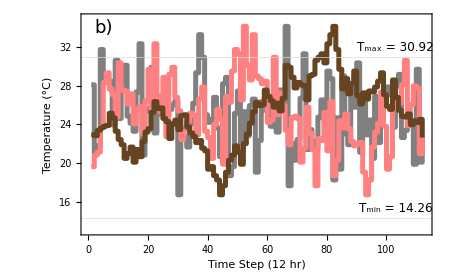

FittedModel[…]

FittedModel[…]

FittedModel[…]

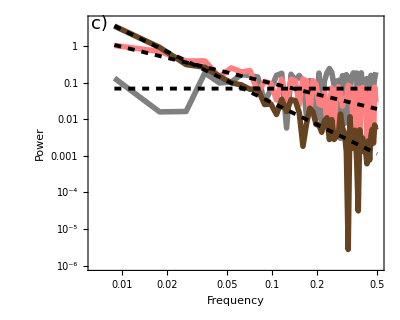

```mathematica
tempsequence={28.105012956566068,20.973777168683974,21.777119582710675,31.756000496201537,28.600816667020446,28.344521382791513,28.47034266137066,23.96687349828974,30.63909206823437,24.607518315140997,27.770735127101812,30.12831827439933,24.843283381565694,24.129453086270793,23.289282561098656,27.360714125686286,32.350579224955645,20.818000065734736,25.63004329427447,25.392481684859003,29.90935651497313,23.110450057296283,25.078338674047963,26.281372248801993,25.235173241485796,24.921661325952037,25.550587396135597,26.03312650171026,26.450446653600267,16.710015292562446,23.549553346399733,22.736717716225108,21.655478617208487,24.048419981102587,26.19796757263583,29.34653377145162,33.289984707437554,30.947121810389547,25.,24.21002216148944,24.52858572096878,26.79954635260587,23.634488914372888,20.65346622854838,28.222880417289325,28.8780378716445,18.690399182412833,19.630578094766086,25.156716618434306,27.460010808216847,21.263503166426503,25.313748228765167,22.832426306719285,25.951580018897413,26.622977130100125,19.052878189610453,22.33516086609751,26.365511085627112,25.47141427903122,26.115237773875315,23.80203242736417,27.263282283774892,23.20045364739413,27.561328293508662,25.709825270812722,34.151719694604665,17.649420775044355,22.009434104564036,20.29191678038176,22.438671706491338,26.710717438901344,31.309600817587167,21.399183332979554,23.463754792880312,22.229264872898188,21.52965733862934,24.764826758514204,26.536245207119688,24.290174729187278,29.521278215385287,28.736496833573497,18.243999503798463,24.686251771234833,19.36090793176563,29.026222831316026,23.01917912323498,21.894987043433932,27.66483913390249,25.78997783851056,30.369421905233914,21.1219621283555,27.167573693280715,22.926540726162184,24.449412603864403,20.478721784614713,26.889549942703717,22.120769481240764,25.870546913729207,26.98082087676502,27.879230518759236,27.073459273837816,23.718627751198007,27.990565895435964,29.181999934265264,22.639285874313714,23.377022869899875,24.36995670572553,23.884762226124685,19.87168172560067,29.70808321961824,20.09064348502687,22.539989191783153};
tempsequence2={19.630578094766086,20.818000065734736,21.1219621283555,23.718627751198007,28.344521382791513,29.34653377145162,27.66483913390249,27.073459273837816,24.764826758514204,30.369421905233914,27.561328293508662,27.460010808216847,26.115237773875315,27.167573693280715,24.048419981102587,25.47141427903122,25.870546913729207,23.01917912323498,26.450446653600267,29.70808321961824,25.63004329427447,32.350579224955645,26.98082087676502,25.313748228765167,28.8780378716445,22.736717716225108,29.181999934265264,29.90935651497313,26.79954635260587,25.392481684859003,22.438671706491338,23.463754792880312,24.290174729187278,25.156716618434306,24.921661325952037,22.926540726162184,26.622977130100125,27.879230518759236,23.289282561098656,22.639285874313714,20.478721784614713,23.96687349828974,25.550587396135597,24.52858572096878,19.87168172560067,26.889549942703717,26.281372248801993,29.521278215385287,31.756000496201537,31.309600817587167,26.536245207119688,34.151719694604665,30.12831827439933,28.600816667020446,33.289984707437554,29.026222831316026,28.736496833573497,28.222880417289325,28.47034266137066,24.21002216148944,24.449412603864403,30.947121810389547,25.,27.263282283774892,25.951580018897413,23.377022869899875,21.894987043433932,24.686251771234833,24.843283381565694,24.607518315140997,20.09064348502687,21.52965733862934,25.78997783851056,23.110450057296283,21.399183332979554,17.649420775044355,22.539989191783153,22.33516086609751,25.235173241485796,21.263503166426503,26.365511085627112,18.690399182412833,20.29191678038176,24.36995670572553,23.634488914372888,25.078338674047963,23.549553346399733,22.229264872898188,21.777119582710675,22.009434104564036,22.120769481240764,19.052878189610453,16.710015292562446,18.243999503798463,21.655478617208487,23.20045364739413,24.129453086270793,27.360714125686286,23.80203242736417,19.36090793176563,20.65346622854838,25.709825270812722,26.710717438901344,26.19796757263583,28.105012956566068,30.63909206823437,23.884762226124685,26.03312650171026,27.990565895435964,27.770735127101812,20.973777168683974,22.832426306719285};
tempsequence3={22.926540726162184,22.832426306719285,23.377022869899875,23.634488914372888,23.80203242736417,23.884762226124685,25.156716618434306,24.686251771234833,23.289282561098656,22.438671706491338,21.894987043433932,20.478721784614713,20.973777168683974,21.655478617208487,20.09064348502687,21.399183332979554,20.65346622854838,22.229264872898188,23.20045364739413,23.549553346399733,25.235173241485796,26.365511085627112,25.63004329427447,25.709825270812722,24.607518315140997,24.290174729187278,22.539989191783153,24.048419981102587,24.449412603864403,23.463754792880312,24.921661325952037,25.,23.718627751198007,23.110450057296283,22.736717716225108,22.120769481240764,22.33516086609751,21.52965733862934,21.263503166426503,19.36090793176563,19.630578094766086,18.690399182412833,18.243999503798463,16.710015292562446,17.649420775044355,19.052878189610453,20.29191678038176,20.818000065734736,21.777119582710675,21.1219621283555,19.87168172560067,22.009434104564036,23.01917912323498,24.129453086270793,25.313748228765167,26.281372248801993,25.951580018897413,26.03312650171026,27.561328293508662,26.889549942703717,26.450446653600267,25.78997783851056,26.19796757263583,25.392481684859003,26.710717438901344,30.12831827439933,29.90935651497313,28.8780378716445,27.770735127101812,28.344521382791513,28.105012956566068,27.990565895435964,26.536245207119688,29.026222831316026,29.181999934265264,30.63909206823437,30.947121810389547,31.309600817587167,30.369421905233914,32.350579224955645,33.289984707437554,34.151719694604665,31.756000496201537,29.70808321961824,27.66483913390249,28.736496833573497,27.167573693280715,28.222880417289325,29.521278215385287,26.98082087676502,26.115237773875315,27.263282283774892,26.622977130100125,27.460010808216847,27.360714125686286,27.879230518759236,28.47034266137066,29.34653377145162,27.073459273837816,25.870546913729207,25.550587396135597,28.600816667020446,26.79954635260587,25.47141427903122,24.843283381565694,24.764826758514204,25.078338674047963,23.96687349828974,24.36995670572553,24.21002216148944,24.52858572096878,22.639285874313714};
Tmax=30.92;
Tmin=14.26;
thickness=.008;
compareseries=ListLinePlot[{tempsequence,tempsequence2,tempsequence3},InterpolationOrder->0,ImageSize->450,PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},GridLines->{None,{Tmin,Tmax}},GridLinesStyle->{Dashed,Thin},(*PlotLegends->Placed[{"γ = 0","γ = 1","γ = 2"},{Left,Bottom}],*)PlotRange->{{-.2,113},{13,35}},Frame->{True,True,False,False},FrameLabel->{"Time Step (12 hr)","Temperature (°C)"},FrameStyle->16,Epilog->{{Text[Style["T_min = 14.26",Black,12],{103,Tmin+1}]},{Text[Style["T_max = 30.92",Black,12],{103,Tmax+1}]},Text[Style["b)",Black,18],{5,34}]}]

n=112;
X=tempsequence;
fftdata=Fourier[X,FourierParameters->{-1,1}];
fftdata=fftdata[[1;;n/2]];
mean=Abs[fftdata[[1]]];
powersp=Table[{i/n,Abs[fftdata[[i+1]]]^2},{i,1,n/2-1}];
phasesp=Table[{i/n,Arg[fftdata[[i+1]]]},{i,1,n/2-1}];
psp1=ListLogLogPlot[powersp,Joined->True,PlotStyle->{Thickness[.01],Gray},PlotRange->{{0.0065,0.51},{.000001,5}},Frame->{True,True,False,False},FrameLabel->{"Frequency","Power"},FrameStyle->16,PlotLegends->Placed[{Style["White noise, γ = 0"(* (-2.66 - .0008x)"*),12,Darker[Gray]]},{Left,Bottom}]];
lm=LinearModelFit[{Log[#1],Log[#2]}&@@@powersp,x,x]
a1=lm[[1,2,1,1]];
b1=lm[[1,2,1,2]];
Show[psp1,LogLogPlot[Exp[a1]*x^b1,{x,1/n,0.5},PlotStyle->{Dashed,Black}]];

X=tempsequence2;
fftdata=Fourier[X,FourierParameters->{-1,1}];
fftdata=fftdata[[1;;n/2]];
mean=Abs[fftdata[[1]]];
powersp=Table[{i/n,Abs[fftdata[[i+1]]]^2},{i,1,n/2-1}];
phasesp=Table[{i/n,Arg[fftdata[[i+1]]]},{i,1,n/2-1}];
psp2=ListLogLogPlot[powersp,Joined->True,PlotStyle->{Thickness[.01],Pink},Frame->{True,True,False,False},FrameLabel->{"Frequency","Power"},FrameStyle->16,PlotLegends->Placed[{Style["Pink noise, γ = 1"(* (-4.64 - 1x)"*),12,Darker[Gray]]},{Left,Bottom}]];
lm=LinearModelFit[{Log[#1],Log[#2]}&@@@powersp,x,x]
a2=lm[[1,2,1,1]];
b2=lm[[1,2,1,2]];
Show[psp2,LogLogPlot[Exp[a2]*x^b2,{x,1/n,0.5},PlotStyle->{Dashed,Black}]];

X=tempsequence3;
fftdata=Fourier[X,FourierParameters->{-1,1}];
fftdata=fftdata[[1;;n/2]];
mean=Abs[fftdata[[1]]];
powersp=Table[{i/n,Abs[fftdata[[i+1]]]^2},{i,1,n/2-1}];
phasesp=Table[{i/n,Arg[fftdata[[i+1]]]},{i,1,n/2-1}];
psp3=ListLogLogPlot[powersp,Joined->True,PlotStyle->{Thickness[.01],Darker[Brown]},Frame->{True,True,False,False},FrameLabel->{"Frequency","Power"},FrameStyle->16,PlotLegends->Placed[{Style["Brown noise, γ = 2" (*(-8.16 - 2x)"*),12,Darker[Gray]]},{Left,Bottom}]];
lm=LinearModelFit[{Log[#1],Log[#2]}&@@@powersp,x,x]
a3=lm[[1,2,1,1]];
b3=lm[[1,2,1,2]];
Show[psp3,LogLogPlot[Exp[a3]*x^b3,{x,1/n,0.5},PlotStyle->{Dashed,Black}]];

powerspectra=Show[psp1,psp2,psp3,LogLogPlot[Exp[a1]*x^b1,{x,1/n,0.5},PlotStyle->{Thickness[.007],Dashed,Black}],LogLogPlot[Exp[a2]*x^b2,{x,1/n,0.5},PlotStyle->{Thickness[.007],Dashed,Black}],LogLogPlot[Exp[a3]*x^b3,{x,1/n,0.5},PlotStyle->{Thickness[.007],Dashed,Black}],FrameStyle->16,ImageSize->400,AspectRatio->.8, Epilog->{Text[Style["c)",Black,18],Scaled[{0.04,0.97}]]}]
```

Once TPC and time series subfigures have run, use this code to create Fig. 2.

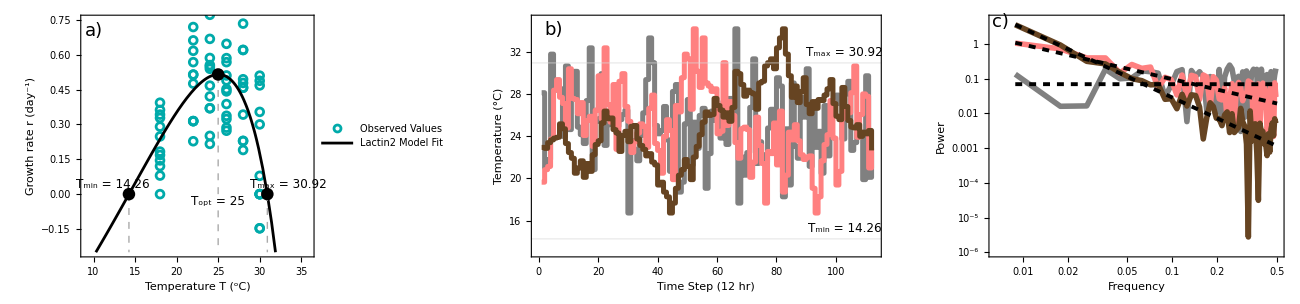

```mathematica
background=GraphicsRow[{TPCplot,compareseries,powerspectra},Spacings->2,ImageSize->1300]
Export[directory<>"Fig2.eps",background,"EPS",ImageResolution->1000];
```